```mathematica
Needs["ErrorBarPlots`"];
(* Be sure to set the correct path *)
SetDirectory[""];
```

```mathematica
MapSpeedup[data_]:=Map[Function[b,
Map[Function[t, N[b[[1]]/t]], b]], data];
```

```mathematica
DoPlot[data_]:=BoxWhiskerChart[Transpose[data], Joined->True, ChartLabels->Range[1,Length[data]], AxesOrigin->{0,0},FrameLabel->{Style["# threads",FontSize->14], Style["speedup", FontSize->14]}](*,PlotLabel->Style["Speedups for matrix benchmark",FontSize->18]]*)
```

```mathematica
DoErrorPlot[data_]:=(meanSpeedups= Map[Mean, Transpose[data]];
stdErrorSpeedups = Map[Function[d,StandardDeviation[d]/Sqrt[Length[d]]], Transpose[data]];plotData = Partition[Riffle[meanSpeedups, stdErrorSpeedups],2];
ErrorListPlot[plotData,Joined->True,AxesOrigin->{0,0}])
```

```mathematica
MakeGrid[data_,threads_]:=Grid[Transpose[{Range[1,threads],Map[Mean, Transpose[data]],Map[StandardDeviation, Transpose[data]]}],Frame->All]
```

```mathematica
matrixLucifer = Import["./matrix/benchmark_results"][[2;;]];
fibonacciLucifer = Import["./fibonacci/benchmark_results"][[2;;]];
loop1Lucifer = Import["./loop1/benchmark_results"][[2;;]];
loop7Lucifer = Import["./loop7/benchmark_results"][[2;;]];
loop21Lucifer = Import["./loop21/benchmark_results"][[2;;]];
```

Import::nffil: File not found during Import.

Part::take: Cannot take positions 2 through -1 in $Failed.

```mathematica
dataLucifer={matrixLucifer, fibonacciLucifer(*, loop1Lucifer*), loop7Lucifer,loop21Lucifer};
speedupsLucifer = MapSpeedup/@dataLucifer;
```

```mathematica
Maxes = Max[Map[Max, Transpose[MapSpeedup[#]]]]&/@dataLucifer
```

{1.51744,1.41151,1.45899,2.77567}

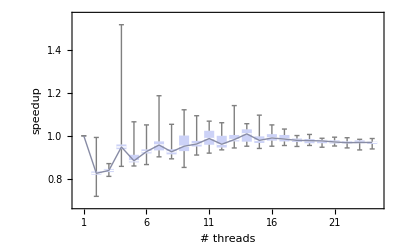

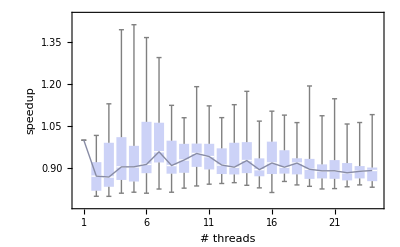

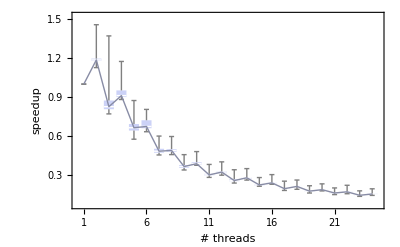

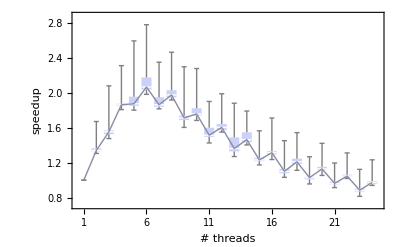

```mathematica
Do[Print[DoPlot[d]],{d,speedupsLucifer}]
```

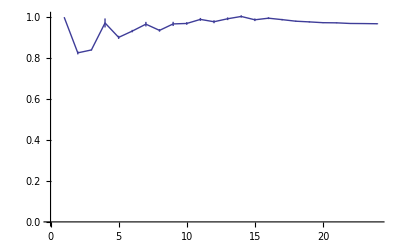

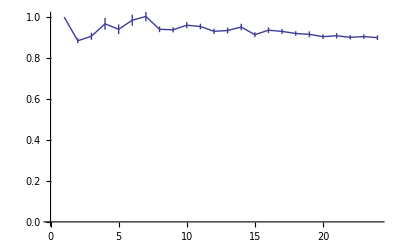

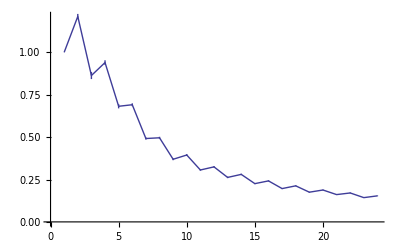

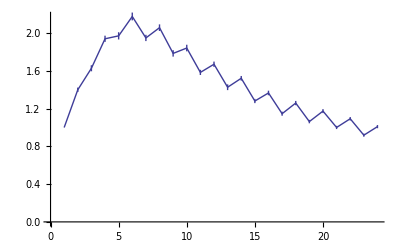

```mathematica
Do[Print[DoErrorPlot[d]],{d,speedupsLucifer}]
```

```mathematica
Do[Print[TeXForm[MakeGrid[d,24]]],{d,dataLucifer}]
```

\begin{array}{ccc}
 1 & 7.84333 & 0.0180676 \\
 2 & 9.52033 & 0.45878 \\
 3 & 9.341 & 0.163335 \\
 4 & 8.156 & 0.715549 \\
 5 & 8.71867 & 0.369816 \\
 6 & 8.42367 & 0.271757 \\
 7 & 8.14833 & 0.450892 \\
 8 & 8.395 & 0.29956 \\
 9 & 8.13567 & 0.450958 \\
 10 & 8.10133 & 0.273858 \\
 11 & 7.941 & 0.312049 \\
 12 & 8.03433 & 0.315558 \\
 13 & 7.91367 & 0.263419 \\
 14 & 7.82267 & 0.235708 \\
 15 & 7.95367 & 0.26592 \\
 16 & 7.88733 & 0.196028 \\
 17 & 7.94133 & 0.151924 \\
 18 & 8.00167 & 0.106061 \\
 19 & 8.02967 & 0.104765 \\
 20 & 8.06133 & 0.0937617 \\
 21 & 8.06733 & 0.0781658 \\
 22 & 8.093 & 0.0896026 \\
 23 & 8.09733 & 0.0989926 \\
 24 & 8.10467 & 0.093725 \\
\end{array}

\begin{array}{ccc}
 1 & 5.60267 & 0.381602 \\
 2 & 6.34433 & 0.281433 \\
 3 & 6.22467 & 0.526411 \\
 4 & 5.89367 & 0.702903 \\
 5 & 6.01767 & 0.529324 \\
 6 & 5.776 & 0.665171 \\
 7 & 5.65233 & 0.621093 \\
 8 & 5.97867 & 0.403756 \\
 9 & 5.98667 & 0.325474 \\
 10 & 5.858 & 0.411762 \\
 11 & 5.89033 & 0.366008 \\
 12 & 6.03367 & 0.301908 \\
 13 & 6.013 & 0.329568 \\
 14 & 5.909 & 0.321552 \\
 15 & 6.136 & 0.235951 \\
 16 & 6.002 & 0.325157 \\
 17 & 6.03033 & 0.20104 \\
 18 & 6.09333 & 0.179623 \\
 19 & 6.13 & 0.228368 \\
 20 & 6.198 & 0.140158 \\
 21 & 6.17433 & 0.184348 \\
 22 & 6.21833 & 0.116266 \\
 23 & 6.193 & 0.0923319 \\
 24 & 6.23167 & 0.121459 \\
\end{array}

\begin{array}{ccc}
 1 & 8.39033 & 0.579158 \\
 2 & 6.92433 & 0.0932806 \\
 3 & 9.80833 & 0.832131 \\
 4 & 8.93733 & 0.257962 \\
 5 & 12.36 & 0.808187 \\
 6 & 12.1557 & 0.583265 \\
 7 & 17.0743 & 0.587207 \\
 8 & 16.9173 & 0.546745 \\
 9 & 22.7473 & 0.765965 \\
 10 & 21.2813 & 0.507725 \\
 11 & 27.4283 & 0.964873 \\
 12 & 25.8767 & 0.836525 \\
 13 & 32.055 & 1.31927 \\
 14 & 29.9717 & 0.768976 \\
 15 & 37.2087 & 1.06901 \\
 16 & 34.7227 & 0.812582 \\
 17 & 42.7503 & 1.23141 \\
 18 & 39.4763 & 1.19352 \\
 19 & 47.9333 & 1.63581 \\
 20 & 44.6253 & 1.12977 \\
 21 & 52.1173 & 1.20143 \\
 22 & 49.2203 & 1.6597 \\
 23 & 58.6313 & 1.39583 \\
 24 & 54.647 & 1.48968 \\
\end{array}

\begin{array}{ccc}
 1 & 6.168 & 0.567757 \\
 2 & 4.40667 & 0.0533908 \\
 3 & 3.8 & 0.189609 \\
 4 & 3.17967 & 0.0257954 \\
 5 & 3.13433 & 0.0908839 \\
 6 & 2.83833 & 0.0957757 \\
 7 & 3.16633 & 0.0787174 \\
 8 & 2.99833 & 0.0523966 \\
 9 & 3.45967 & 0.087749 \\
 10 & 3.35267 & 0.0824593 \\
 11 & 3.89667 & 0.105384 \\
 12 & 3.69333 & 0.0879394 \\
 13 & 4.33767 & 0.20015 \\
 14 & 4.05433 & 0.121249 \\
 15 & 4.81833 & 0.0944707 \\
 16 & 4.518 & 0.0984501 \\
 17 & 5.38733 & 0.138637 \\
 18 & 4.903 & 0.133885 \\
 19 & 5.80567 & 0.116964 \\
 20 & 5.25833 & 0.124377 \\
 21 & 6.166 & 0.102001 \\
 22 & 5.644 & 0.0704468 \\
 23 & 6.71833 & 0.16297 \\
 24 & 6.11133 & 0.111099 \\
\end{array}